```mathematica
SetDirectory["C:/Users/serha/OneDrive/Masaüstü/MyRepo/master_thesis_MMT003/210714_finalising/fxd_bounds"];
```

```mathematica
Get["../../algoritm_packages/SingleNetworks-algorithm-package-2.wl"]
(* ?SingleNetworks`* *)
```

```mathematica
stoichioforhomosapiens=Drop[Import["../../210324_disc_time_windows_and_OR_model/iAT_PLT_636_stoichiomat.csv",HeaderLines->1],None,{1}];
SparseArray@stoichioforhomosapiens
```

SparseArray[…]

```mathematica
stoichiometricmatrix=stoichioforhomosapiens;
metabolites=738;
fluxexchanges=1008;
steadystatevector=ConstantArray[{0,0},metabolites];
first[a_]:=First/@GatherBy[Ordering@a,a[[#]]&]//Sort;
```

```mathematica
case="bounds";
intvalues={-1,1};
interval2="-5+5_quadrupled";

interval="50percentdecreased_("<>ToString@intvalues[[1]]<>","<>ToString@intvalues[[2]]<>")";
subsetpositionsforsequences=Import["../cases/subsetpositionsforsequences_half.mx"];
boundaries=Import["../cases/boundaries_for_deleted_reaction_series_-5and5_quadrupled.mx"];
boundariespos0=Table[Position[boundaries[[i]],{0,0}],{i,10}];
boundariesposval=Table[Position[boundaries[[i]],{-5,5}],{i,10}];
boundariesa=Table[ReplacePart[(Table[ReplacePart[ConstantArray[{-500,500},fluxexchanges],MapThread[#1->#2&,{boundariespos0[[i]],ConstantArray[{0,0},Length@boundariespos0[[i]]]}]],{i,10}])[[j]],MapThread[#1->#2&,{boundariesposval[[j]],ConstantArray[{-5,5},Length@boundariesposval[[j]]]}]],{j,10}];
```

```mathematica
syntheticseqgenerator[stoichiometricmatrix_,steadystatevector_,boundaries_,fluxexchanges_,subsetpositions_]:=Module[{coefficients,objectivefunctions,solutionvectors},
coefficients=Table[RandomReal[intvalues,Length@subsetpositions],50];
objectivefunctions=Table[ReplacePart[ConstantArray[0.,fluxexchanges],MapThread[#1->#2&,{subsetpositions,coefficients[[i]]}]],{i,50}];
solutionvectors=Chop[Table[LinearProgramming[-objectivefunctions[[i]],stoichiometricmatrix,steadystatevector,boundaries],{i,Length@objectivefunctions}],10^-5];{objectivefunctions,solutionvectors}]
```

```mathematica
(*AbsoluteTiming[resultset=Table[Quiet@Table[syntheticseqgenerator[stoichiometricmatrix,steadystatevector,j,fluxexchanges,i],{i,subsetpositionsforsequences}],{j,boundariesa}];]*)
```

```mathematica
(*Export["C:/Users/serha/NonDrive/OR_model-25.06.2021/solution_vectors/"<>interval<>"solutionvectors_fxd"<>case<>"_-5and5_quadrupled.mx",Table[Flatten[resultset[[i]][[All,2]],1],{i,10}]]

Export["C:/Users/serha/NonDrive/OR_model-25.06.2021/objective_functions/"<>interval<>"objfunc_fxd"<>case<>"_-5and5_quadrupled.mx",Table[Flatten[resultset[[i]][[All,1]],1],{i,10}]]*)
```

```mathematica
(*solutionvectorslist=Table[Flatten[resultset[[i]][[All,2]],1],{i,10}];
objfunctionslist=Table[Flatten[resultset[[i]][[All,1]],1],{i,10}];*)
```

```mathematica
solutionvectorslist=Import["C:/Users/serha/NonDrive/OR_model-25.06.2021/solution_vectors/"<>interval<>"solutionvectors_fxd"<>case<>"_-5and5_quadrupled.mx"];
objfunctionslist=Import["C:/Users/serha/NonDrive/OR_model-25.06.2021/objective_functions/"<>interval<>"objfunc_fxd"<>case<>"_-5and5_quadrupled.mx"];
```

LinearProgramming::lpipncv: The interior point algorithm cannot converge to the tolerance of 1.49012×10^-8. The best residual achieved is 0.000170396. The failure to converge might be because the problem is mildly infeasible. Setting the option Method -> RevisedSimplex should give a more definite answer, though large problems may take longer computing time.

```mathematica
AbsoluteTiming[featuredatalist=Table[MapThread[Dot,{objfunctionslist[[j]],solutionvectorslist[[j]]}],{j,10}];]
```

{3.67409,Null}

LinearProgramming::lpipncv: The interior point algorithm cannot converge to the tolerance of 1.49012×10^-8. The best residual achieved is 0.000170396. The failure to converge might be because the problem is mildly infeasible. Setting the option Method -> RevisedSimplex should give a more definite answer, though large problems may take longer computing time.

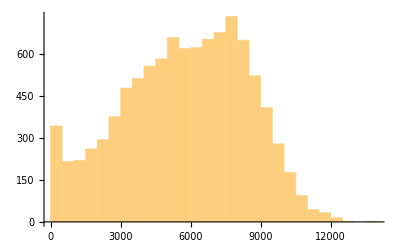
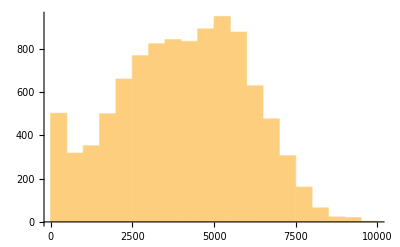
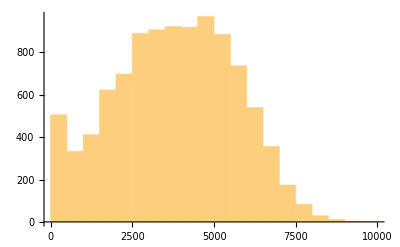
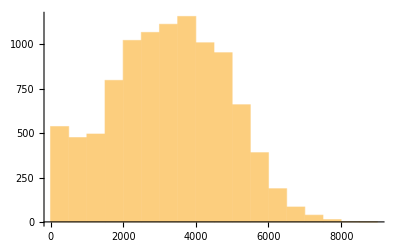
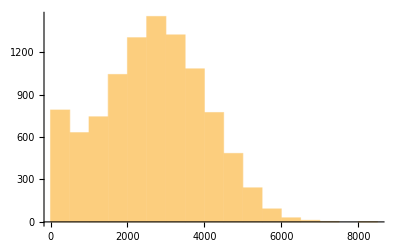
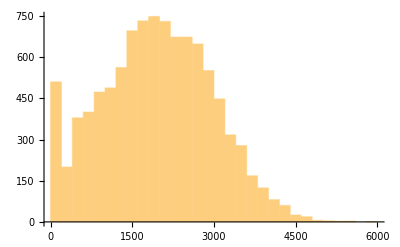
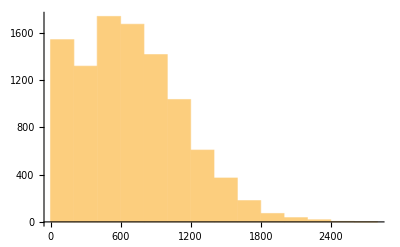
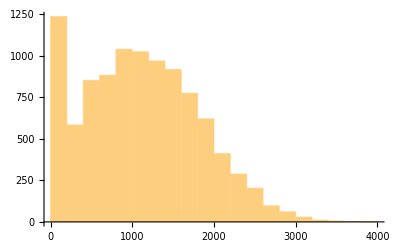

```mathematica
datafulllist=Table[Join[Partition[Range@10000,1],Partition[Flatten@Table[ConstantArray[i,50],{i,200}],1],Partition[featuredatalist[[j]],1],2],{j,10}];
Table[Histogram@datafulllist[[i]][[All,3]],{i,10}]
```

```mathematica
thread={{1,300},{2,220},{3,210},{4,210},{5,190},{6,140},{7,60},{8,90},{9,75},{10,85}};
N@Mean@thread[[All,2]]
```

158.

```mathematica
thread=Thread[{Range@10,505}]
```

{{1,505},{2,505},{3,505},{4,505},{5,505},{6,505},{7,505},{8,505},{9,505},{10,505}}

```mathematica
AbsoluteTiming[widthdataFixedstep2=Table[snetworkdatabinned[3,i[[2]],datafulllist[[i[[1]]]]],{i,thread}];]
```

{271.06,Null}

```mathematica
graphsandnodenumbers12=Table[snetworkgraph[widthdataFixedstep2[[i]][[1]],widthdataFixedstep2[[i]][[2]],2,7,400,Green],{i,10}];
graphsandnodenumbers12[[All,2]]
```

{27,20,19,18,16,12,6,8,7,8}

```mathematica
modularityvalues12=Table[N@GraphAssortativity[graphsandnodenumbers12[[i]][[1]],FindGraphCommunities[graphsandnodenumbers12[[i]][[1]]],"Normalized"->False],{i,Length@graphsandnodenumbers12}];
```

```mathematica
singlerandomgraphsdegfxd12=Table[randomizinggraphdegfxd[i],{i,graphsandnodenumbers12[[All,1]]}];
singlerandomerdrenmodularityvalues12=Table[N@GraphAssortativity[singlerandomgraphsdegfxd12[[i]],FindGraphCommunities[singlerandomgraphsdegfxd12[[i]]],"Normalized"->False],{i,Length@singlerandomgraphsdegfxd12}];
singlerandomgraphscomm12=Table[randomizinggraphmod[i],{i,graphsandnodenumbers12[[All,1]]}];
singlerandomcommmodularityvalues12=Table[N@GraphAssortativity[singlerandomgraphscomm12[[i]],FindGraphCommunities[singlerandomgraphscomm12[[i]]],"Normalized"->False],{i,Length@singlerandomgraphscomm12}];
```

```mathematica
AbsoluteTiming[Zscoresmodularity12=Table[zscorefunctionfortwonullmodels[i],{i,graphsandnodenumbers12[[All,1]]}];]
```

{125.643,Null}

```mathematica
bucketnode12=graphsandnodenumbers12[[All,2]]
```

{27,20,19,18,16,12,6,8,7,8}

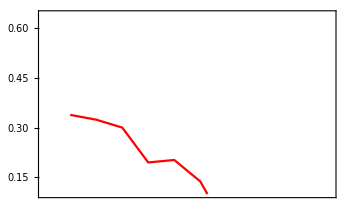
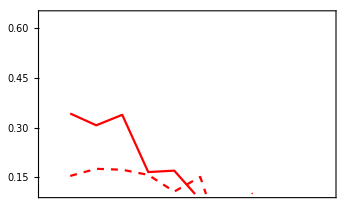
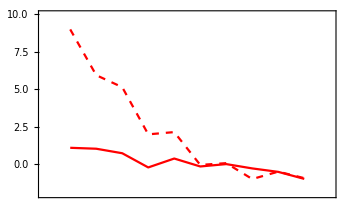

```mathematica
modularityvaluestimewinsmall=modularityvalues12;
randommodtimewinsmalldegreefxd=singlerandomerdrenmodularityvalues12;
randommodtimewinsmallcomm=singlerandomcommmodularityvalues12;
Zscoretimewinsmall=Zscoresmodularity12;
modularityplotrange={0.1,0.64};
(*MinMax[{modularityvalues1,singlerandomcommmodularityvalues1,singlerandomerdrenmodularityvalues1,modularityvalues12}]*)
padding=38;
win2=10;
Row[{ListLinePlot[Thread[{Range@win2,modularityvaluestimewinsmall}],Frame->True,ImagePadding->padding,FrameTicks->{{All,None},{None,All}},FrameLabel->{{None,None},{None,Style["Time Windows",Red]}},PlotStyle->Red,ImageSize->350,PlotRange->{{0,win2+1},modularityplotrange}],
Row[{ListLinePlot[{Thread[{Range@win2,randommodtimewinsmalldegreefxd}],Thread[{Range@win2,randommodtimewinsmallcomm}]},Frame->True,ImagePadding->padding,FrameTicks->{{All,None},{None,All}},FrameLabel->{{None,None},{None,Style["Time Windows",Red]}},PlotStyle->{{Dashed,Red},Red},ImageSize->350,PlotRange->{{0,win2+1},modularityplotrange}],
ListLinePlot[{Thread[{Range@win2,Zscoretimewinsmall[[All,1]]}],Thread[{Range@win2,Zscoretimewinsmall[[All,2]]}]},Frame->True,ImagePadding->padding,FrameTicks->{{All,None},{None,All}},FrameLabel->{{None,None},{None,Style["Time Windows",Red]}},PlotStyle->{{Dashed,Red},Red},ImageSize->350,PlotRange->{{0,win2+1},MinMax[Flatten[Zscoretimewinsmall],1]}]}],LineLegend[{Dashed,Black},{"Degrees Fixed N.M.","Modularity N.M."},LegendMargins->0,LegendMarkerSize->{20,20}],Spacer@0.1}]
```

```mathematica
AbsoluteTiming[widthdataFixedbucket2=Table[snetworkdatafxdbucket[3,bucketnode12[[i]],datafulllist[[i]]],{i,10}];]
```

{142.015,Null}

```mathematica
graphsandnodenumbers32=Table[snetworkgraph[widthdataFixedbucket2[[i]][[1]],widthdataFixedbucket2[[i]][[2]],1.5,7,400,Green],{i,10}];
modularityvalues32=Table[N@GraphAssortativity[graphsandnodenumbers32[[i]][[1]],FindGraphCommunities[graphsandnodenumbers32[[i]][[1]]],"Normalized"->False],{i,Length@graphsandnodenumbers32}];
```

```mathematica
singlerandomgraphsdegfxd32=Table[randomizinggraphdegfxd[i],{i,graphsandnodenumbers32[[All,1]]}];
singlerandomerdrenmodularityvalues32=Table[N@GraphAssortativity[singlerandomgraphsdegfxd32[[i]],FindGraphCommunities[singlerandomgraphsdegfxd32[[i]]],"Normalized"->False],{i,Length@singlerandomgraphsdegfxd32}];
singlerandomgraphscomm32=Table[randomizinggraphmod[i],{i,graphsandnodenumbers32[[All,1]]}];
singlerandomcommmodularityvalues32=Table[N@GraphAssortativity[singlerandomgraphscomm32[[i]],FindGraphCommunities[singlerandomgraphscomm32[[i]]],"Normalized"->False],{i,Length@singlerandomgraphscomm32}];
```

```mathematica
AbsoluteTiming[Zscoresmodularity32=Table[zscorefunctionfortwonullmodels[i],{i,graphsandnodenumbers32[[All,1]]}];]
```

{53.0595,Null}

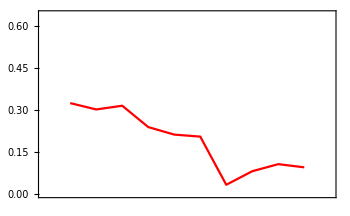
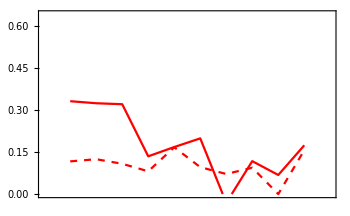
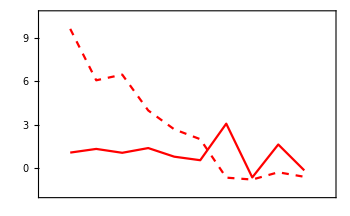

```mathematica
modularityvaluestimewinsmall=modularityvalues32;
randommodtimewinsmalldegreefxd=singlerandomerdrenmodularityvalues32;
randommodtimewinsmallcomm=singlerandomcommmodularityvalues32;
Zscoretimewinsmall=Zscoresmodularity32;
modularityplotrange={0,0.64};
(*MinMax[{modularityvalues1,singlerandomcommmodularityvalues1,singlerandomerdrenmodularityvalues1,modularityvalues12}]*)
padding=38;
win2=10;
Row[{ListLinePlot[Thread[{Range@win2,modularityvaluestimewinsmall}],Frame->True,ImagePadding->padding,FrameTicks->{{All,None},{None,All}},FrameLabel->{{None,None},{None,Style["Time Windows",Red]}},PlotStyle->Red,ImageSize->350,PlotRange->{{0,win2+1},modularityplotrange}],
Row[{ListLinePlot[{Thread[{Range@win2,randommodtimewinsmalldegreefxd}],Thread[{Range@win2,randommodtimewinsmallcomm}]},Frame->True,ImagePadding->padding,FrameTicks->{{All,None},{None,All}},FrameLabel->{{None,None},{None,Style["Time Windows",Red]}},PlotStyle->{{Dashed,Red},Red},ImageSize->350,PlotRange->{{0,win2+1},modularityplotrange}],
ListLinePlot[{Thread[{Range@win2,Zscoretimewinsmall[[All,1]]}],Thread[{Range@win2,Zscoretimewinsmall[[All,2]]}]},Frame->True,ImagePadding->padding,FrameTicks->{{All,None},{None,All}},FrameLabel->{{None,None},{None,Style["Time Windows",Red]}},PlotStyle->{{Dashed,Red},Red},ImageSize->350,PlotRange->{{0,win2+1},MinMax[Flatten[Zscoretimewinsmall],1]}]}],LineLegend[{Dashed,Black},{"Degrees Fixed N.M.","Modularity N.M."},LegendMargins->0,LegendMarkerSize->{20,20}],Spacer@0.1}]
```

```mathematica
Export["plot_values/fxd_"<>case<>"/"<>interval<>"_"<>interval2<>"-modularityvalues-fss.mx",modularityvalues12]
Export["plot_values/fxd_"<>case<>"/"<>interval<>"_"<>interval2<>"-singrand-erd-modularityvalues-fss.mx",singlerandomerdrenmodularityvalues12]
Export["plot_values/fxd_"<>case<>"/"<>interval<>"_"<>interval2<>"-singrand-comm-modularityvalues-fss.mx",singlerandomcommmodularityvalues12]
Export["plot_values/fxd_"<>case<>"/"<>interval<>"_"<>interval2<>"-zscores-fss.mx",Zscoresmodularity12]
Export["plot_values/fxd_"<>case<>"/"<>interval<>"_"<>interval2<>"-modularityvalues-fbs.mx",modularityvalues32]
Export["plot_values/fxd_"<>case<>"/"<>interval<>"_"<>interval2<>"-singrand-erd-modularityvalues-fbs.mx",singlerandomerdrenmodularityvalues32]
Export["plot_values/fxd_"<>case<>"/"<>interval<>"_"<>interval2<>"-singrand-comm-modularityvalues-fbs.mx",singlerandomcommmodularityvalues32]
Export["plot_values/fxd_"<>case<>"/"<>interval<>"_"<>interval2<>"-zscores-fbs.mx",Zscoresmodularity32]
```

plot_values/fxd_bounds/50percentdecreased_(-1,1)_-5+5_quadrupled-modularityvalues-fss.mx

plot_values/fxd_bounds/50percentdecreased_(-1,1)_-5+5_quadrupled-singrand-erd-modularityvalues-fss.mx

plot_values/fxd_bounds/50percentdecreased_(-1,1)_-5+5_quadrupled-singrand-comm-modularityvalues-fss.mx

plot_values/fxd_bounds/50percentdecreased_(-1,1)_-5+5_quadrupled-zscores-fss.mx

plot_values/fxd_bounds/50percentdecreased_(-1,1)_-5+5_quadrupled-modularityvalues-fbs.mx

plot_values/fxd_bounds/50percentdecreased_(-1,1)_-5+5_quadrupled-singrand-erd-modularityvalues-fbs.mx

plot_values/fxd_bounds/50percentdecreased_(-1,1)_-5+5_quadrupled-singrand-comm-modularityvalues-fbs.mx

plot_values/fxd_bounds/50percentdecreased_(-1,1)_-5+5_quadrupled-zscores-fbs.mx